# Ecuaciones diferenciales autónomas

La ecuación logística, o modelo de Verhulst, está dada por

Su espacio fase es:

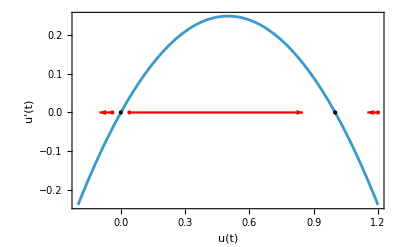

```mathematica
Show[Plot[u*(1-u),{u,-0.2,1.2},Frame->{True,True,False,False},FrameLabel->{u[t],TraditionalForm[D[u[t],t]]},Epilog->{PointSize[Medium],Point[{{0,0},{1,0}}]}],NumberLinePlot[Interval[{-Infinity,-0.04}],{x,-0.1,-0.04},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{0.04,Infinity}],{x,0.04,0.85},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,1.2}],{x,1.15,1.2},PlotStyle->Red,Spacings->0]]
```

Las soluciones como funciones de  se ven como

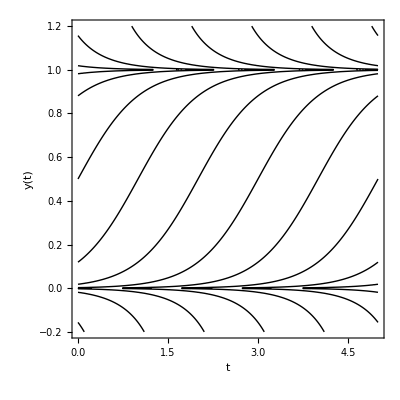

```mathematica
ContourPlot[-2*t+Log[Abs[y]]-Log[Abs[1-y]],{t,0,5},{y,-0.2,1.2},ContourShading->None,Contours->10,PlotPoints->100,FrameLabel->{t,y[t]}]
```